# ANN Simulation

This is done only for the cross evaluation, as it is the most useful

## Importing Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/ff278/Desktop/Lutein_Experiment

```mathematica
(*Type 1 Network*)
(*Against set 1,2 4*)
(*For Test cases  the Rows are in order, from left to right
Index (1)
Illumination DCW nitrate lutein for the experimental data (2,3,4,5)
Illumination DCW nitrate lutein for the 12 step (6,7,8,9)
Illumination DCW nitrate lutein for the 24 step (10,11,12,13)
Illumination DCW nitrate lutein for the 36 step (14,15,16,17)
Illumination DCW nitrate lutein for the 72 step (18,19,20,21)*
From left to Right they are set 1, 2 and 4*)
```

```mathematica
(*Lutein thus is index 5,9,13,17,21*)
```

```mathematica
IntervalsLength={{0,12,24,36,48,60,72,84,96,108,120,132},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}
{{0,12,24,36,48,60,72,84,96,108,120,132,144},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}
(*Type 2 Network*)
(*Against set 1,2 4*)
(*For Test cases  the rows are in order, from up to down
Illumination DCW nitrate lutein for the experimental data (2,3,4,5)
Illumination DCW nitrate lutein for the simulated data (6,7,8,9)*
From up to down they are set 1, 2 and 4.
Lutein is 5 and 9*)

lutInd2={5,10}
nitInd2={4,9}
DCWInd2={3,8}
```

{{0,12,24,36,48,60,72,84,96,108,120,132},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}

{{0,12,24,36,48,60,72,84,96,108,120,132,144},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}

{5,10}

{4,9}

{3,8}

```mathematica
ValT2H1Cross=DeleteCases[Import["data/Lutein_NN_Type2H1_CrossVal_Both_Less_ExpTraj_Rescale2.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN1A=Part[ValT2H1Cross,lutInd2];
NIT1A=Part[ValT2H1Cross,nitInd2];
DCW1A=Part[ValT2H1Cross,DCWInd2];
```

```mathematica
(*The two cross validation sets*)
```

```mathematica
RealLut1=LUTEIN1A[[1]][[;;12]];
RealNit1=NIT1A[[1]][[;;12]];
RealDCW1=DCW1A[[1]][[;;12]];
RealLut2=LUTEIN1A[[1]][[13;;]];
RealNit2=NIT1A[[1]][[13;;]];
RealDCW2=DCW1A[[1]][[13;;]];
```

```mathematica
LUTEINA1=LUTEIN1A[[2]][[;;12]];
NITA1=NIT1A[[2]][[;;12]];
DCWA1=DCW1A[[2]][[;;12]];
LUTEINB1=LUTEIN1A[[2]][[13;;]];
NITB1=NIT1A[[2]][[13;;]];
DCWB1=DCW1A[[2]][[13;;]];
```

```mathematica
RealLutA1=Table[{IntervalsLength[[1,i]],RealLut1[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitA1=Table[{IntervalsLength[[1,i]],RealNit1[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWA1=Table[{IntervalsLength[[1,i]],RealDCW1[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealLutB1=Table[{IntervalsLength[[1,i]],RealLut2[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitB1=Table[{IntervalsLength[[1,i]],RealNit2[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWB1=Table[{IntervalsLength[[1,i]],RealDCW2[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

```mathematica
CROSSLUT1A=Table[{IntervalsLength[[1,i]],LUTEINA1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1A=Table[{IntervalsLength[[1,i]],NITA1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1A=Table[{IntervalsLength[[1,i]],DCWA1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSLUT1B=Table[{IntervalsLength[[1,i]],LUTEINB1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1B=Table[{IntervalsLength[[1,i]],NITB1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1B=Table[{IntervalsLength[[1,i]],DCWB1[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

```mathematica
(*Against set 3*)
ValT2H1CrossVal=DeleteCases[Import["data/Lutein_NN_Type2H1_CrossVal_Both_Less_SimTraj_Rescale2.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN5A=Part[ValT2H1CrossVal,lutInd2][[2]];
NIT5A=Part[ValT2H1CrossVal,nitInd2][[2]];
DCW5A=Part[ValT2H1CrossVal,DCWInd2][[2]];
```

```mathematica
LUTEINA5=LUTEIN5A[[;;12]];
NITA5=NIT5A[[;;12]];
DCWA5=DCW5A[[;;12]];
LUTEINB5=LUTEIN5A[[13;;]];
NITB5=NIT5A[[13;;]];
DCWB5=DCW5A[[13;;]];
```

```mathematica
CROSSLUT5A=Table[{IntervalsLength[[1,i]],LUTEINA5[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT5A=Table[{IntervalsLength[[1,i]],NITA5[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW5A=Table[{IntervalsLength[[1,i]],DCWA5[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSLUT5B=Table[{IntervalsLength[[1,i]],LUTEINB5[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT5B=Table[{IntervalsLength[[1,i]],NITB5[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW5B=Table[{IntervalsLength[[1,i]],DCWB5[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

```mathematica
ValT2H2CrossVal=DeleteCases[Import["data/Lutein_NN_Type2H2_CrossVal_Both_Less_ExpTraj_Rescale2.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN7A=Part[ValT2H2CrossVal,lutInd2][[2]];
NIT7A=Part[ValT2H2CrossVal,nitInd2][[2]];
DCW7A=Part[ValT2H2CrossVal,DCWInd2][[2]];
```

```mathematica
LUTEINA7=LUTEIN7A[[;;12]];
NITA7=NIT7A[[;;12]];
DCWA7=DCW7A[[;;12]];
LUTEINB7=LUTEIN7A[[13;;]];
NITB7=NIT7A[[13;;]];
DCWB7=DCW7A[[13;;]];
```

```mathematica
CROSSLUT7A=Table[{IntervalsLength[[1,i]],LUTEINA7[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT7A=Table[{IntervalsLength[[1,i]],NITA7[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW7A=Table[{IntervalsLength[[1,i]],DCWA7[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSLUT7B=Table[{IntervalsLength[[1,i]],LUTEINB7[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT7B=Table[{IntervalsLength[[1,i]],NITB7[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW7B=Table[{IntervalsLength[[1,i]],DCWB7[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

```mathematica
ValT2H2CrossVal=DeleteCases[Import["data/Lutein_NN_Type2H2_CrossVal_Both_Less_SimTraj_Rescale2.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN8A=Part[ValT2H2CrossVal,lutInd2][[2]];
NIT8A=Part[ValT2H2CrossVal,nitInd2][[2]];
DCW8A=Part[ValT2H2CrossVal,DCWInd2][[2]];
```

```mathematica
LUTEINA8=LUTEIN8A[[;;12]];
NITA8=NIT8A[[;;12]];
DCWA8=DCW8A[[;;12]];
LUTEINB8=LUTEIN8A[[13;;]];
NITB8=NIT8A[[13;;]];
DCWB8=DCW8A[[13;;]];
```

```mathematica
CROSSLUT8A=Table[{IntervalsLength[[1,i]],LUTEINA8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8A=Table[{IntervalsLength[[1,i]],NITA8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8A=Table[{IntervalsLength[[1,i]],DCWA8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSLUT8B=Table[{IntervalsLength[[1,i]],LUTEINB8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8B=Table[{IntervalsLength[[1,i]],NITB8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8B=Table[{IntervalsLength[[1,i]],DCWB8[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

## Plotting Data

### Lutein

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
(*Type 1, 1 Layer*)
```

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

```mathematica
(*1 Hidden layer*)
```

```mathematica
(*Expected value from experimental point*)
```

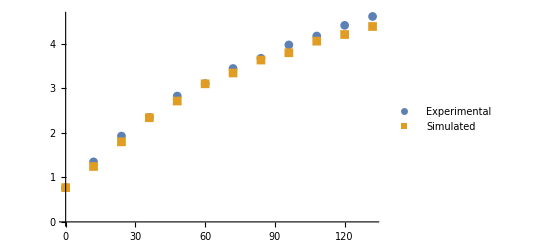

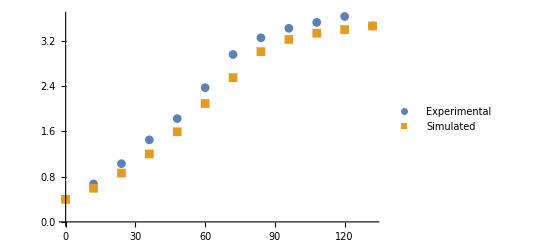

```mathematica
ListPlot[{RealLutA1,CROSSLUT1A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealLutB1,CROSSLUT1B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*Fully Simulated Trajectory*)
```

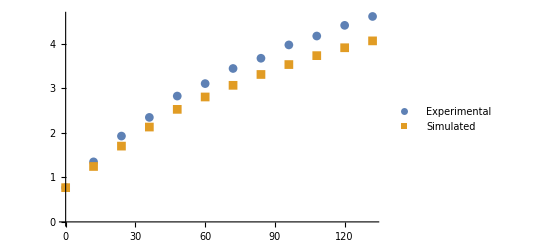

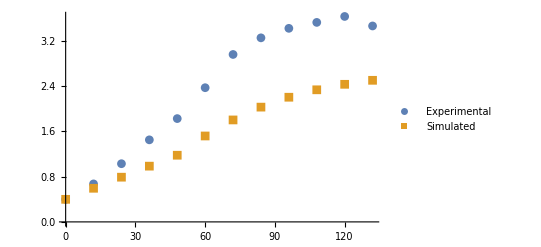

```mathematica
ListPlot[{RealLutA1,CROSSLUT5A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealLutB1,CROSSLUT5B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*2 Hidden Layers*)
```

```mathematica
(*From Experimental points*)
```

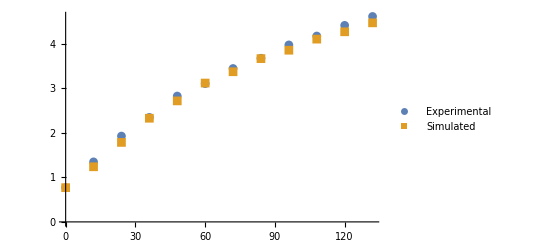

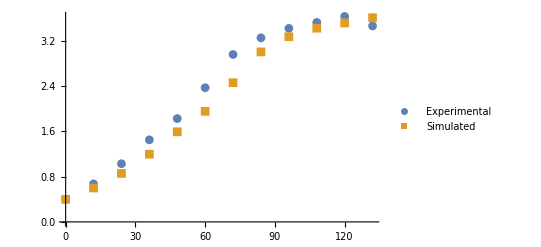

```mathematica
ListPlot[{RealLutA1,CROSSLUT7A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealLutB1,CROSSLUT7B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*Fully Simulated Trajectory*)
```

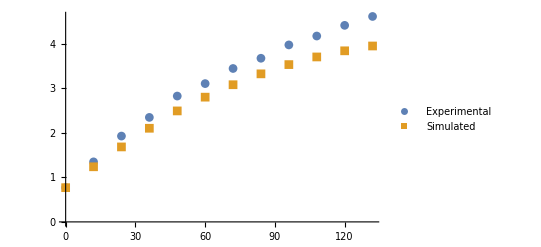

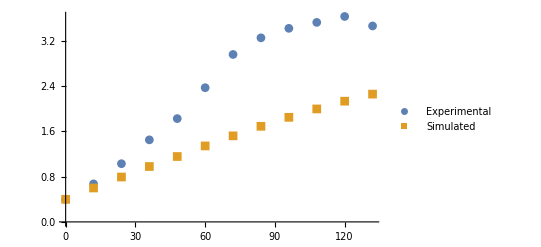

```mathematica
ListPlot[{RealLutA1,CROSSLUT8A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealLutB1,CROSSLUT8B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

### Nitrogen

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
(*Type 1, 1 Layer*)
```

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

```mathematica
(*1 Hidden layer*)
```

```mathematica
(*Expected value from experimental point*)
```

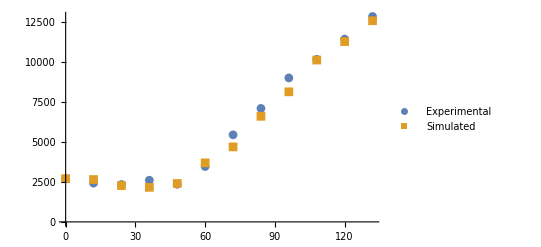

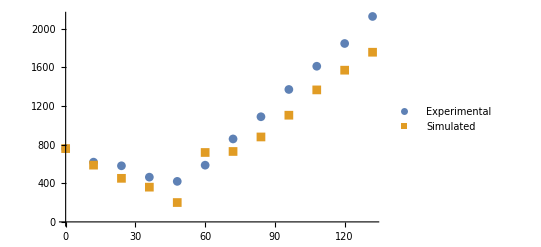

```mathematica
ListPlot[{RealNitA1,CROSSNIT1A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealNitB1,CROSSNIT1B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*Fully Simulated Trajectory*)
```

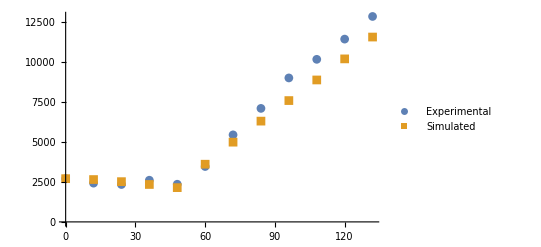

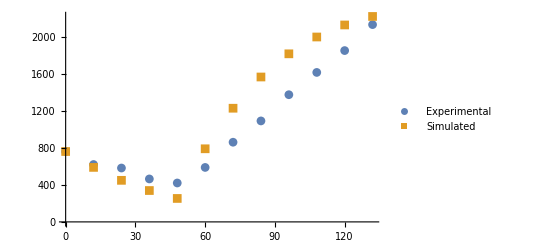

```mathematica
ListPlot[{RealNitA1,CROSSNIT5A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealNitB1,CROSSNIT5B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*2 Hidden Layers*)
```

```mathematica
(*From Experimental points*)
```

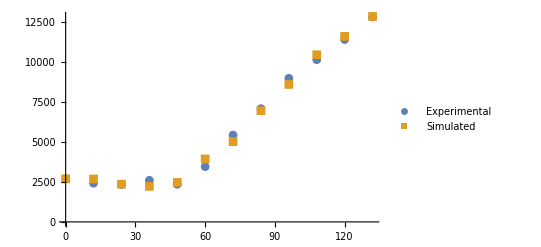

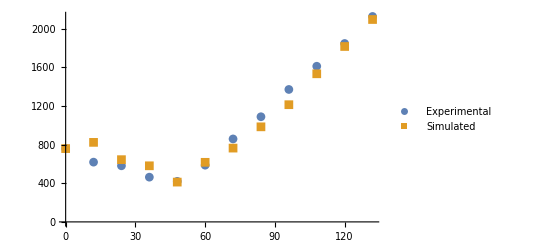

```mathematica
ListPlot[{RealNitA1,CROSSNIT7A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealNitB1,CROSSNIT7B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*Fully Simulated Trajectory*)
```

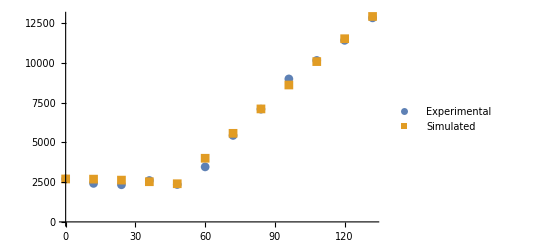

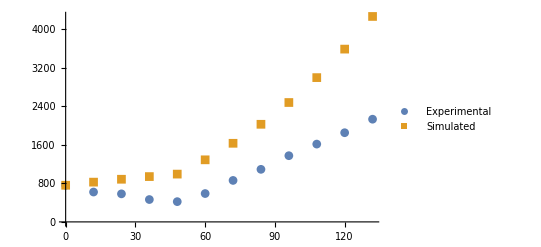

```mathematica
ListPlot[{RealNitA1,CROSSNIT8A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealNitB1,CROSSNIT8B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

### DCW

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
(*Type 1, 1 Layer*)
```

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

```mathematica
(*1 Hidden layer*)
```

```mathematica
(*Expected value from experimental point*)
```

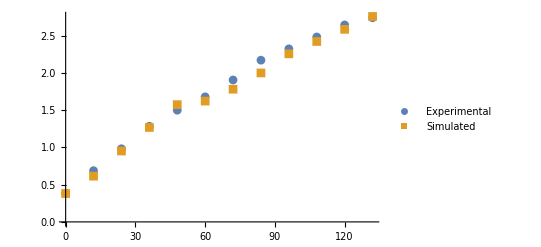

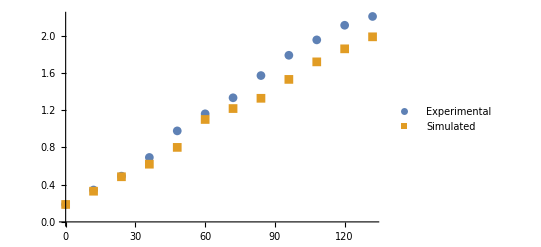

```mathematica
ListPlot[{RealDCWA1,CROSSDCW1A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealDCWB1,CROSSDCW1B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*Fully Simulated Trajectory*)
```

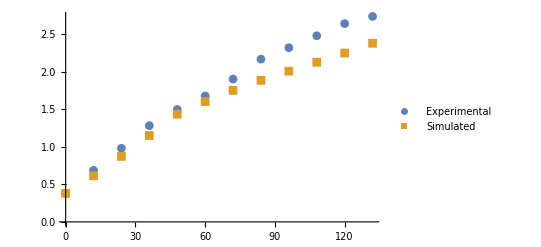

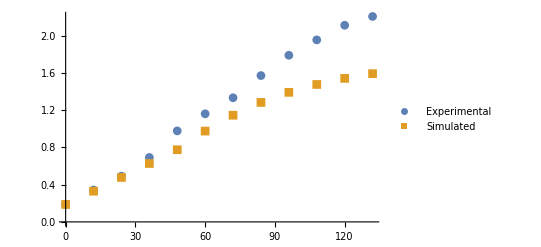

```mathematica
ListPlot[{RealDCWA1,CROSSDCW5A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealDCWB1,CROSSDCW5B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*2 Hidden Layers*)
```

```mathematica
(*From Experimental points*)
```

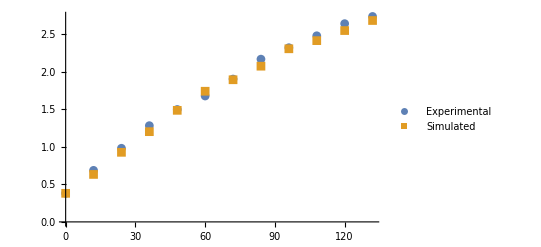

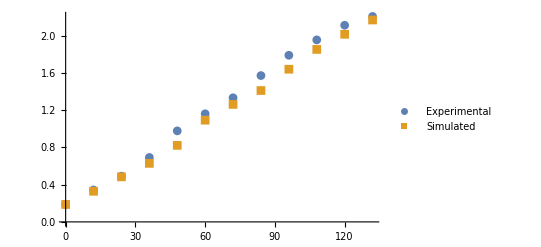

```mathematica
ListPlot[{RealDCWA1,CROSSDCW7A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealDCWB1,CROSSDCW7B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

```mathematica
(*Fully Simulated Trajectory*)
```

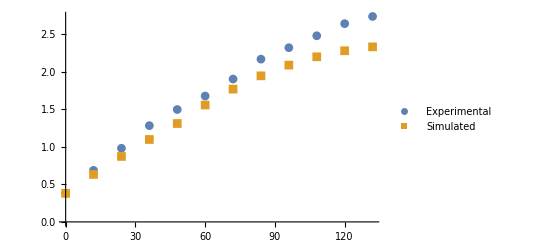

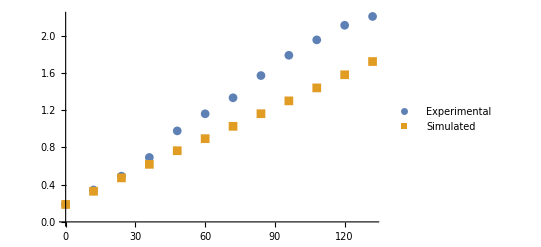

```mathematica
ListPlot[{RealDCWA1,CROSSDCW8A},PlotMarkers->Automatic,PlotLegends->legendLab2]
ListPlot[{RealDCWB1,CROSSDCW8B},PlotMarkers->Automatic,PlotLegends->legendLab2]
```